# Experiment 33 - The Stern-Gerlach Experiment

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* We enter our peak position data and format it for analysis with CurveFit. *)
zmax={{"S Detector_current(10^-13A)","Delta_z"},{0.459,15.540-14.570},{0.459,15.520-14.560},{0.459,15.510-14.570},{1.203,15.480-14.860},{1.203,15.450-14.830},{1.203,15.420-14.832},{0.341,15.300-14.550},{0.341,15.280-14.570},{0.341,15.320-14.550},{0.851,15.730-14.310},{0.851,15.710-14.330},{0.851,15.720-14.280},{2.183,15.900-13.900},{2.183,15.600-13.750},{2.183,15.958-13.950}};
profile851={{"S Detector_current","peak_position(mm)"},{0.68,15.000},{0.70,14.800},{0.80,14.600},{0.90,14.400},{0.90,14.200},{0.90,14.000},{0.70,15.200},{0.82,15.400},{0.90,15.600},{0.92,15.800},{0.90,16.000}};
profile0={{"S Detector_current","peak_position(mm)"},{2.17,15.000},{1.85,15.200},{1.25,15.400},{0.90,15.600},{0.80,15.800},{0.77,16.000},{1.80,14.800},{1.30,14.600},{0.90,14.400},{0.80,14.200},{0.70,14.000}};
Export["zmax.dat",zmax];
Export["profile851.dat",profile851];
Export["profile0.dat",profile0];
```

## 0-Field Profile

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/profile0.dat

File comment header:

Detector_current	peak_position(mm)

LoadFile::sorted: Data sorted in increasing x order.

Read 11 data points.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[0.025 ](* We assign an uncertainty of 0.025 mA to our detector current profile as a function of position, due to the smallest division on the calibrated voltmeter corresponding to 0.05 mA. *)
```

11 σy values replaced.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{14.1055,16.0417}

n= 10

1 point removed.

```mathematica
GaussianCFit[]
```

n = 10

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
1.38167 | c= 
0.77297 | 
σ_y_max= 
0.0219111 | σ_c= 
0.0148731 | 
μ= 
15.0004 | sigma= 
0.277922 | 
σ_μ= 
0.00444361 | σ_sigma= 
0.00624063 | Std. deviation= 
0.0245073

Fit of (x,y±σ_y)

y_max= 
1.38167 | c= 
0.77297 | 
σ_y_max= 
0.0223511 | σ_c= 
0.0151737 | 
μ= 
15.0004 | sigma= 
0.277922 | 
σ_μ= 
0.00453293 | σ_sigma= 
0.00636805 | χ^2/(n-4)= 
0.960973

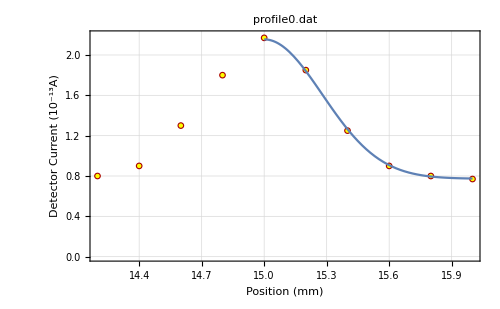
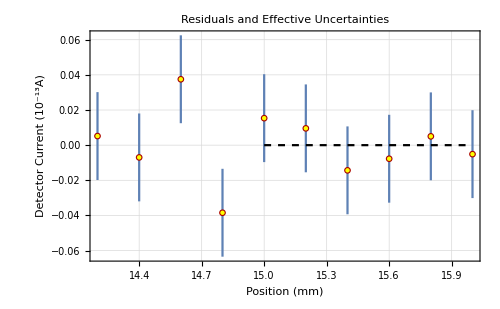
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
1.38167 | c= 
0.77297 | 
σ_y_max= 
0.0223511 | σ_c= 
0.0151737 | 
μ= 
15.0004 | sigma= 
0.277922 | 
σ_μ= 
0.00453293 | σ_sigma= 
0.00636805 | χ^2/(n-4)= 
0.960973

```mathematica
LinearDifferencePlot[FrameLabel->{"Position (mm)", "Detector Current (10^-13A)"}]
```

```mathematica
(* I am unsure as to why CurveFit refuses to plot half of the fitted function, but we have obtained σ and observe a reasonably good χ̃ 2. *)
```

## Processing data

### Convolved Z_max corrected to theoretical value

```mathematica
data=Import["/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/zmax.dat"]
```

{{S,Detector_current(mA),Delta_z},{0.459,0.97},{0.459,0.96},{0.459,0.94},{1.203,0.62},{1.203,0.62},{1.203,0.588},{0.341,0.75},{0.341,0.71},{0.341,0.77},{0.851,1.42},{0.851,1.38},{0.851,1.44},{2.183,2.},{2.183,1.85},{2.183,2.008}}

```mathematica
zmaxdata=Table[{data[[i]][[1]],(data[[i]][[2]])/2},{i,2,Length[data]}]
```

{{0.459,0.485},{0.459,0.48},{0.459,0.47},{1.203,0.31},{1.203,0.31},{1.203,0.294},{0.341,0.375},{0.341,0.355},{0.341,0.385},{0.851,0.71},{0.851,0.69},{0.851,0.72},{2.183,1.},{2.183,0.925},{2.183,1.004}}

```mathematica
σ=0.277922
```

0.277922

```mathematica
solveTable=Table[ZconvMax[0.2+0.001z,σ],{z,1500}];
```

```mathematica
solver[obs_]:=0.2+0.001*Flatten[Position[Abs[solveTable-obs],_?(#<0.001&)]][[1]]
```

```mathematica
modifiedZmax=Join[{{"S Detector_current(10^-13A)","Corrected_Zmax(mm)"}},Table[{zmaxdata[[i]][[1]],solver[zmaxdata[[i]][[2]]]},{i,1,Length[zmaxdata]}]]
```

{{S Detector_current(10^-13A),Corrected_Zmax(mm)},{0.459,0.356},{0.459,0.352},{0.459,0.344},{1.203,0.261},{1.203,0.261},{1.203,0.256},{0.341,0.286},{0.341,0.277},{0.341,0.291},{0.851,0.563},{0.851,0.542},{0.851,0.573},{2.183,0.867},{2.183,0.788},{2.183,0.871}}

```mathematica
Export["/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/corrected_Zmax.dat",modifiedZmax]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/corrected_Zmax.dat

### Coil current data transformed to B_z data

```mathematica
data=Import["/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/corrected_Zmax.dat"]
```

{{S,Detector_current(10^-13A),Corrected_Zmax(mm)},{0.459,0.356},{0.459,0.352},{0.459,0.344},{1.203,0.261},{1.203,0.261},{1.203,0.256},{0.341,0.286},{0.341,0.277},{0.341,0.291},{0.851,0.563},{0.851,0.542},{0.851,0.573},{2.183,0.867},{2.183,0.788},{2.183,0.871}}

```mathematica
modData=Join[{data[[1]]},Table[{B[data[[i]][[1]]],data[[i]][[2]]},{i,2,Length[data]}]]
```

{{S,Detector_current(10^-13A),Corrected_Zmax(mm)},{0.539632,0.356},{0.539632,0.352},{0.539632,0.344},{0.985027,0.261},{0.985027,0.261},{0.985027,0.256},{0.430783,0.286},{0.430783,0.277},{0.430783,0.291},{0.821991,0.563},{0.821991,0.542},{0.821991,0.573},{1.19494,0.867},{1.19494,0.788},{1.19494,0.871}}

```mathematica
Export["/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/finalZmax.dat",modData]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/finalZmax.dat

## Position of peaks

Having obtained σ = 0.27792mm for the Gaussian zero-field beam, we can use the Mathematica notebook provided for the Stern-Gerlach experiment to correct our data for z_max to the theoretical z_max for a 0-width beam. The new data is saved, and we then use the Magnetic field calculator provided to transform our current values into B-field values. This processed data is save, and can be used for the analysis:

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/finalZmax.dat

File comment header:

Detector_current(10^-13A)	Corrected_Zmax(mm)

LoadFile::sorted: Data sorted in increasing x order.

Read 15 data points.

```mathematica
CalculateYsigmas[]
```

Sorted data in order of increasing X values.

Calculated and assigned Y uncertainties.

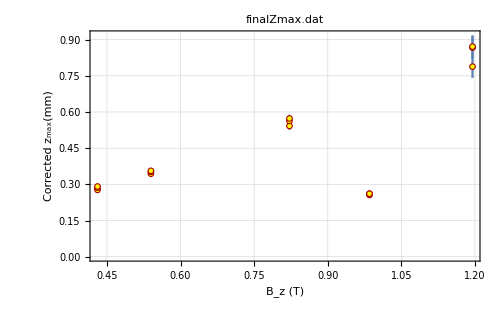

```mathematica
LinearDataPlot[FrameLabel->{"B_z (T)","Corrected z_max(mm)"}]
```

We observe an outlier, which we have to remove seeing as including it prevents us from doing any sort of linear fit. It is probably due to measurement error, seeing as the delayed response makes it difficult to reliably identify a peak, and makes it easy to mistake small fluctuations for features in the detector current profile. 

Even with the outlier removed, we can observe an increase in the uncertainty as B_zincreases: as the peaks become broader, it becomes difficult to reliably find the peaks using the analog voltmeter.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to remove." ]}, 
  Print[x]; 

  XRangeRemove[Sequence@@x] 
]
```

{0.9478,0.9972}

n= 12

3 points removed.

```mathematica
(* We now carry out a linear fit on our data. *)
```

```mathematica
LinearFit[]
```

n = 12

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.0397507 | b= 
0.734989 | 
σ_a= 
0.0183515 | σ_b= 
0.0228488 | Std. deviation= 
0.0233866

Fit of (x,y±σ_y)

a= 
-0.0247287 | b= 
0.705271 | 
σ_a= 
0.0114416 | σ_b= 
0.021234 | χ^2/(n-2)= 
1.3031

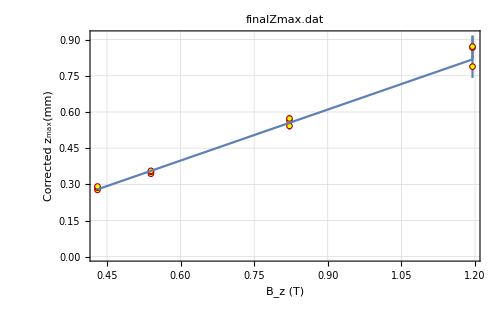
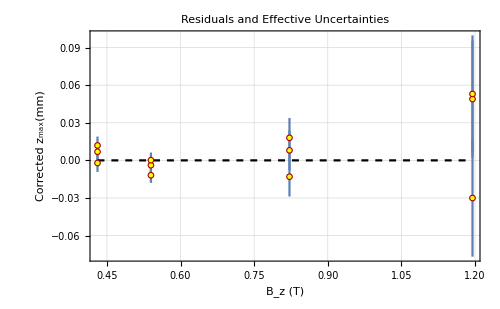
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.0247287 | b= 
0.705271 | 
σ_a= 
0.0114416 | σ_b= 
0.021234 | χ^2/(n-2)= 
1.3031

```mathematica
LinearDifferencePlot[FrameLabel->{"B_z (T)","Corrected z_max(mm)"}]
```

We observe a reasonably good (χ̃)^2 of 1.30, and an offset of -0.0025±0.0014 mm, consistent with zero within the 10% error in our calibration. Therefore, our results agree up to accuracy with the prediction that z_max is linear in B.

### Estimating μ_B

We expect z_max=μ_B/3[l_2(l_2/2+l_3)1/(2 k T)]1.76 B_z. We can then estimate μ_Bby μ_B=(6k T b)/(1.76[l_2(l_2/2+l_3)]) where b is the slope of our linear fit.

```mathematica
l2=12.7 (* cm *);
l3=7.9 (* cm *);
k=1.3806*10^-16 (* erg K^-1 *);
T=(273+116) (* K*);
b={0.00000705271,0.00000021234} (* cm G^-1 *);
μ[b_]:=(6 k T b)/(1.76(l2(l2/2+l3)))(* erg G^-1 *)
NumberForm[μb=μ[b],3]
```

{7.13×10^-21,2.15×10^-22}

In SI units, this corresponds to μ_B=(7.13 ± 0.21) × 10^-24J T^-1. However, we now need to account for the uncertainty in our calibration for converting coil current to B-field data. This corresponds to a 10% uncertainty in our proportionality factor, which we add in quadrature to the uncertainty in μ_B:

```mathematica
μb[[2]]=μb[[1]]*Sqrt[(μb[[2]]/μb[[1]])^2+(0.10)^2];
NumberForm[μb,3]
```

{7.13×10^-21,7.45×10^-22}

We therefore obtain μ_B=(7.13 ± 0.75) × 10^-24J T^-1 as our estimate for μ_B. We observe that this is within 3 standard errors of the literature value of 9.274 × 10^-24J T^-1. To accuracy of the experiment, our results therefore do not allow us to reject the hypothesis that z_max=μ_B/3[l_2(l_2/2+l_3)1/(2 k T)]1.76 B_z.

However, we have a large standard error (~ 11%) in our estimate, which is indicative of uncertainties inherent to the experiment (uncertainty in calibration, notably, along with the uncertainties associated with the apparatus such as the divisions on the detector voltmeter) and due to the quality of the data (experimental errors in finding peaks due to the delayed response). Furthermore, we have a sparse dataset, which does not allow our analysis to confirm the hypothesis with reasonable confidence.

## Non-zero magnetic field beam profile

We load a non-zero magnetic field beam profile for coil current = 0.851 A, which by our calibration corresponds to 0.822 T. We use our model to predict the Z-distribution:

```mathematica
μbval=9.274*10^-21 (* erg G^-1 *);
bz=8220(* G *);
zmaxprofile=(μbval 1.76)/(6 k T)(l2(l2/2+l3))bz (* cm *)
```

0.0753532

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/profile851.dat

File comment header:

Detector_current	peak_position(mm)

LoadFile::sorted: Data sorted in increasing x order.

Read 11 data points.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

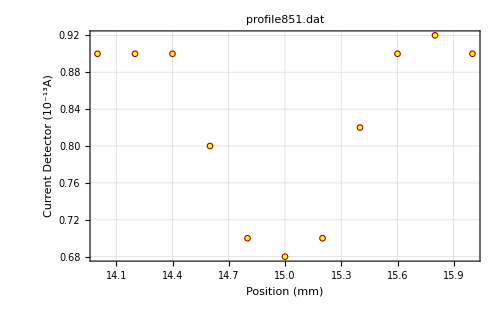

```mathematica
LinearDataPlot[FrameLabel->{"Position (mm)", "Current Detector (10^-13A)"}]
```

```mathematica
(* We use the provided Notebook to create a table of values for the theoretical distribution with finite width σ = 0.2779 mm, Subscript[z, max] =0.753 mm. For a Gaussian, σ = 0.2779 mm corresponds to a FWHM of 0.6544 mm. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/theoretical851.dat

Read 201 data points.

```mathematica
(* We scale and shift the data to be able to compare the theoretical distribution with our dataset. *)
```

```mathematica
?CurveFit`DataTransform
```

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := x +15
ynew[ x_, y_ ] := y/(0.252-0.0486)(0.92-0.68)+(0.68-0.0486)-0.01

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 201 points transformed.

```mathematica
With[  {name = SystemDialogInput["FileSave", DataFileName]},
  If[ name =!= $Canceled, SaveFile[name]]
]
```

Sorted data saved in /home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 33/scaled_theoretical851.dat

```mathematica
scaledTheoretical=DeleteCases[Import["scaled_theoretical851.dat"],0.,Infinity];
```

```mathematica
distribution=Interpolation[scaledTheoretical];
```

```mathematica
profile=Drop[Import["profile851.dat"],1];
flipped=Table[{profile[[i]][[2]],profile[[i]][[1]]},{i,1,Length[profile]}];
```

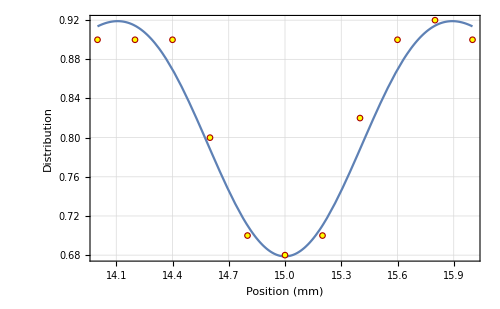

```mathematica
plt1=Plot[distribution[x],{x,14,16},PlotRange->All];
plt2=ListPlot[flipped];
Show[plt1,plt2,FrameLabel->{"Position (mm)","Distribution"}]
```

We have found parameters for our model to match our non-zero profile at coil current of 0.851 A, then offset and scaled our theoretical predictions to match our measurements for the profile (distribution as a function of position). We then used an interpolating function to recover the theoretical distribution, and plotted it against our measured profile.

We observe that the qualitative shape matches quite well. However, the peaks appear wider and z_maxappears larger in the theoretical distribution than in our measurement. This is probably due to error in calibration of the magnet, but may also be due to an error in our determination of σ (for instance, if we took the profile while the B-field was not quite zeroed), which we have used to calculate the convolved Z-distribution above.